```mathematica
Clear["Global`*"]
```

```mathematica
f[λ_,r_,Δ_,t_,z_]:=Evaluate[FullSimplify[F[z,t]/.First[DSolve[{λ (r (z-1)^2-1/2 Δ (z^2-1)) D[F[z,t], z]==D[F[z,t], t],F[z,0]==z},F,{z,t}]],Assumptions->{λ>0,r>0,r<1/2,Δ>0,t≥0}]]
f0[λ_,r_,Δ_,t_,z_]:=Evaluate[Limit[f[λ,r,δ,t,z],δ->0]]
```

```mathematica
g[λ_,r_,Δ_,t_,z_]:=Evaluate[z Exp[λ Δ (20-1) Integrate[f[λ,r,Δ,τ,z]-1,{τ,0,t},Assumptions->{λ>0,r>0,r<1/2,Δ>0,t≥0}]]]
```

```mathematica
h[λ_,r_,Δ_,t_,z_]:=19/20 f[λ,r,Δ,t,z]+1/20 g[λ,r,Δ,t,z]
```

```mathematica
p[f_,λ_,r_,Δ_,t_,M_]:=InverseFourier[Table[f[λ,r,Δ,t,Exp[(2 π ⅈ n)/M]],{n,0,M-1}]]/(√M)
```

```mathematica
condPb[{p0_,ps___}]:={ps}/(1-p0)
```

```mathematica
cumprob[ps_]:=1-FoldList[Plus,0,ps]
```

```mathematica
Limit[D[f[λ,r,Δ,t,z], z],z->1]
```

ⅇ^(-t Δ λ)

```mathematica
FullSimplify[Limit[D[g[λ,r,Δ,t,z], z],z->1],Assumptions->{λ>0,r>0,r<1/2,Δ>0,t≥0}]
```

20-19 ⅇ^(-t Δ λ)

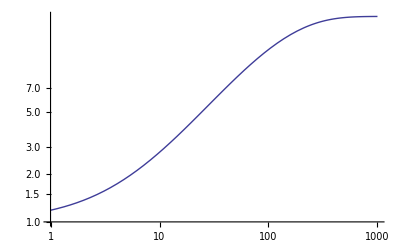

```mathematica
LogLogPlot[1/(1-h[0.77,0.25,0.01,t,0]),{t,1,1000}]
```

```mathematica
1/(1-f0[λ,r,Δ,t,0]) // FullSimplify
```

1+r t λ

```mathematica
SeriesCoefficient[f0[λ,r,Δ,t,z],{z,0,m}];
FullSimplify[% / (1-%/.m->0),Assumptions->{m∈Integers, m≥1}]
1-Sum[%,{m,1,n}]
```

((r t λ)/(1+r t λ))^m/(r t λ)

((r t λ)/(1+r t λ))^n

```mathematica
condPb[p[f0,0.77,1/4,1/100,3,31]]
```

{0.633914,0.232067,0.0849564,0.0311013,0.0113857,0.00416815,0.0015259,0.00055861,0.000204499,0.0000748642,0.0000274067,0.0000100332,3.67301×10^-6,1.34464×10^-6,4.92252×10^-7,1.80206×10^-7,6.59709×10^-8,2.4151×10^-8,8.84133×10^-9,3.23668×10^-9,1.1849×10^-9,4.33776×10^-10,1.58799×10^-10,5.81341×10^-11,2.12821×10^-11,7.79105×10^-12,2.85219×10^-12,1.04415×10^-12,3.82275×10^-13,1.39929×10^-13}

```mathematica
cumprob[condPb[p[f0,0.77,1/4,1/100,3,31]]]
```

{1,0.366086,0.134019,0.0490623,0.017961,0.00657526,0.00240711,0.000881208,0.000322597,0.000118098,0.0000432341,0.0000158274,5.79417×10^-6,2.12116×10^-6,7.76527×10^-7,2.84275×10^-7,1.04069×10^-7,3.80981×10^-8,1.39471×10^-8,5.10579×10^-9,1.8691×10^-9,6.84201×10^-10,2.50425×10^-10,9.16257×10^-11,3.34915×10^-11,1.22095×10^-11,4.41835×10^-12,1.56619×10^-12,5.22027×10^-13,1.39777×10^-13,-2.22045×10^-16}

```mathematica
hplot=ListLogPlot[Table[MapThread[{#1,#2}&,{Range[0,Floor[10 t]] (1-h[0.77,1/4,1/100,t,0]),cumprob[condPb[p[h,0.77,1/4,1/100,t,Floor[10 t]+1]]]}],{t,{3/7,10/7,3,6,12,26,52}}],PlotRange->{{0,5},{1/10^3,1}}];
```

```mathematica
fplot=ListLogPlot[Table[MapThread[{#1,#2}&,{Range[0,Floor[10 t]] (1-f0[0.77,1/4,1/100,t,0]),cumprob[condPb[p[f0,0.77,1/4,1/100,t,Floor[10 t]+1]]]}],{t,{3/7,10/7,3,6,12,26,52}}],Joined->True,PlotRange->{{0,5},{1/10^3,1}}];
```

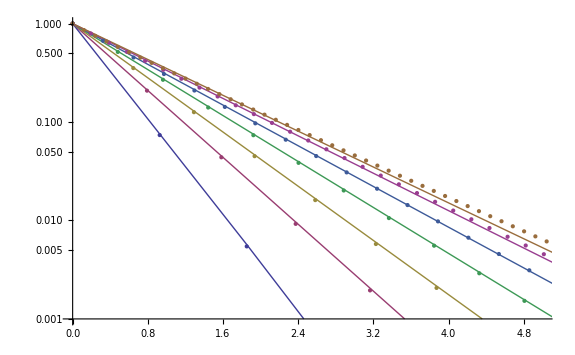

```mathematica
Show[fplot,hplot]
```

```mathematica
gf[λ_,r_,Δ_,ρ_,z_]:=2^(-(2 Δ (1/ρ-1))/(-2 r+Δ)) ((2 r-2 r z+Δ+z Δ)/Δ)^((2 Δ (1/ρ-1))/(-2 r+Δ))
```

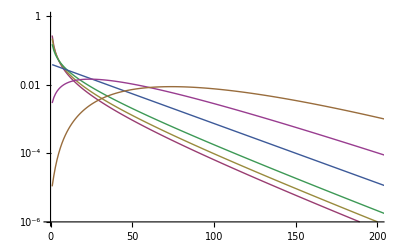

```mathematica
ListLogPlot[Table[Tooltip[MapThread[{#1,#2}&,{Range[1,Floor[400]],condPb[p[gf,0.77,1/4,1/100,1/n,401]]}],n],{n,{1,2,5,10,25.5,50,100}}],Joined->True,PlotRange->{{0,200},{10^-6,1}}]
```

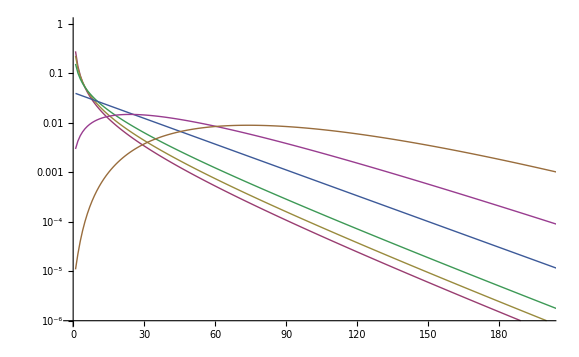

-Graphics-